This notebook implements the BasicFunctions package to generate random density matrices and shows probability of transitions as evolved under a pulse for some length of time. This notebook also displays the BlochPlot function. 
-Peter Gartin

```mathematica
(* Defining operations *)
Run[<<"C:\\Users\\peter\\Documents\\Research\\qi-functions\\BasicFunctions.wls"]
```

1

```mathematica
{(RandomDensityMatrix[5]//Tr)==1,
RandomDensityMatrix[5]//HermitianMatrixQ,
RandomDensityMatrix[5]//PositiveSemidefiniteMatrixQ,
RandomDensityMatrix[5]//DensityMatrixQ}
```

{True,True,True,True}

```mathematica
Boole[{True,True,True,True}]
```

{1,1,1,1}

```mathematica
RandomDensityMatrix[2]
```

{{0.348167+0. ⅈ,-0.188656+0.323296 ⅈ},{-0.188656-0.323296 ⅈ,0.651833+0. ⅈ}}

```mathematica
testH[t_]:=IdentityMatrix[2];
```

```mathematica
BlochPlot[RandomDensityMatrix[2],testH,0,2]
```

-Graphics3D-

```mathematica
BlochListPlot[list__,args___]:=Block[{points},
points=BlochVector/@TT;
ListPointPlot3D[points,BoxRatios->{1, 1, 1}]];
```

```mathematica
TT=Table[RandomDensityMatrix[2],{i,1,1000}];
```

```mathematica
BlochListPlot[TT]
```

-Graphics3D-

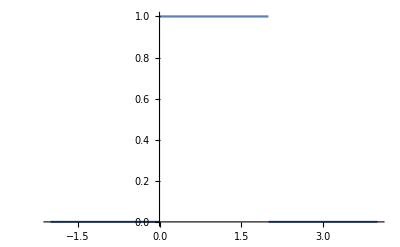

```mathematica
Plot[UnitStep[t]-UnitStep[t-2],{t,-2,4}]
```

```mathematica
SquarePulseHamiltonian[τ_,Ω_,ω_,E0_,E1_,t_]:=Block[{H0=E0 {{1},{0}}.{{1,0}}+E1{{0},{1}}.{{0,1}},Hp=Ω Cos[ω t]({{1},{0}}.{{0,1}}+{{0},{1}}.{{1,0}})},H0+Hp( UnitStep[t]- UnitStep[t-τ])];
```

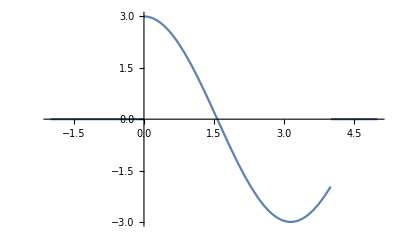

```mathematica
Plot[SquarePulseHamiltonian[4,3,1,0,1,t][[1,2]],{t,-2,5},PlotRange->All]
```

```mathematica
SquarePulseHamiltonian[1,2,3,0,1,t]
```

{{0,2 Cos[3 t] (-UnitStep[-1+t]+UnitStep[t])},{2 Cos[3 t] (-UnitStep[-1+t]+UnitStep[t]),1}}

```mathematica
Soln=SquarePulseSoln[6,1,1,0,1];
Soln[10]//MatrixForm
```

(-0.923017-0.0313636 ⅈ | 0.0266628-0.38255 ⅈ
0.230487+0.306481 ⅈ | 0.757414-0.528456 ⅈ)

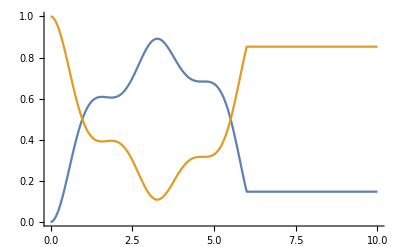

```mathematica
Plot[{TransitionProbibility[t,Soln,2,1],TransitionProbibility[t,Soln,1,1]},{t,0,10},PlotRange->All]
```

```mathematica
A=EvolveDensityMatrix[RandomDensityMatrix[2],Soln,3];
{(A//Tr),
A//HermitianMatrixQ,
A//PositiveSemidefiniteMatrixQ,
A//DensityMatrixQ}
```

{0.999999,True,True,True}

```mathematica
BlochVector[EvolveDensityMatrix[RandomDensityMatrix[2],Soln,3]]
```

{0.582616,0.158787,0.79441}

```mathematica
BlochPlot[RandomDensityMatrix[2],Soln,0,10]
```

-Graphics3D-